# Analysis of Triangle Completion Categorical experiment

## Loading the data and functions

```mathematica
SetDirectory["/home/uvhart/GitHubLib/Four_Experiments_Combined"];
```

```mathematica
SetDirectory["/Users/alcarden4/Desktop/WebstormProjects/Four_Experiments_Combined"]
```

```mathematica
Needs["ErrorBarPlots`"];
LogFilePilotB2A30=DeleteCases[Import["b.2A30_logVertexCat.txt","Table"],Except[{___,"ERROR",___}]];
LogFilePilotB2A60=DeleteCases[Import["b.2A60_logVertexCat.txt","Table"],Except[{___,"ERROR",___}]];
LogFilePilotB1A30=DeleteCases[Import["b1A30_logVertexCat.txt","Table"],Except[{___,"ERROR",___}]];
LogFilePilotB1A60=DeleteCases[Import["b1A60_logVertexCat.txt","Table"],Except[{___,"ERROR",___}]];
(*LogFileExp1=DeleteCases[Import["logVertexCatExp.txt","Table"],Except[{___,"ERROR",___}]];*)
```

```mathematica
TotalExpData=Join[LogFilePilotB2A30,LogFilePilotB2A60,LogFilePilotB1A30,LogFilePilotB1A60];
```

#### Data

```mathematica
NumOfQuestions=8;
OverHead=9;
TotalEntries=NumOfQuestions+OverHead;
DataUnCln={TotalExpData[[;;,;;2]],TotalExpData[[;;,6;;]]}ᵀ;
DATA=Join[#[[1]],If[Length[#[[2]]]==1,StringSplit[#[[2,1]],"_"],Join[StringSplit[#[[2,1]],"_"],#[[2,2;;]]]]]&/@DataUnCln;
DATASort=Select[Select[GatherBy[DATA,#[[3]]&],Length@#≥ TotalEntries&],ToExpression@Cases[#,{__,"age",__}][[1,5]]<99&];
DataClean={Flatten@{#[[2,{3,5}]],#[[3,5]],#[[4,5]],#[[5,5]]},SortBy[#,#[[{1,2}]]&]&@GatherBy[Select[#,StringContainsQ[#[[5]],"Run"]&][[2;;,{7,9,11,12,13,15,17,19}]],#[[{1,2}]]&]}&/@DATASort;
(*ID,gender,age,right/left handed,education*)
(*7=angle; 9=base factor; 11=Qtype; 12=Manipulation; 13=What's manipulated; 15=correct answer; 17=timing; 19=user answer;*)
DataClnGraded=Join@@@Map[Append[#,If[#[[6]]==#[[8]],1,0]]&,DataClean[[;;,2]],{3}];
```

```mathematica
rules={{"angle","increase","distance"}-> 1,{"angle","decrease","distance"}-> 2,{"angle","increase","angle"}-> 3,{"angle","decrease","angle"}->4,{"vertex","increase","distance"}->5,{"vertex","decrease","distance"}-> 6,{"vertex","increase","angle"}-> 7,{"vertex","decrease","angle"}-> 8};
QuestionType={"AID","ADD","AIA","ADA","VID","VDD","VIA","VDA"};
AnswerRules={"downward"-> 1,"stayPlace"-> 2,"upward"-> 3,"smaller"-> 1,"same"-> 2,"bigger"-> 3};
```

All questions together

```mathematica
DataCleanAll=({Flatten@{#[[2,{3,5}]],#[[3,5]],#[[4,5]],#[[5,5]]},Select[#,StringContainsQ[#[[5]],"Run"]&][[2;;,{7,9,11,12,13,15,17,19}]]}&/@DATASort);
DataCleanAllGraded=Map[Append[#,If[#[[6]]==#[[8]],1,0]]&,DataCleanAll[[;;,2]],{2}];
```

## Percent Correct

### Percent correct vs. Base length

```mathematica
(*1=angle; 2=base factor; 3=Qtype; 4=Manipulation; 5=What's manipulated; 6=correct answer; 7=timing; 8=user answer; 9=correct/not*)
```

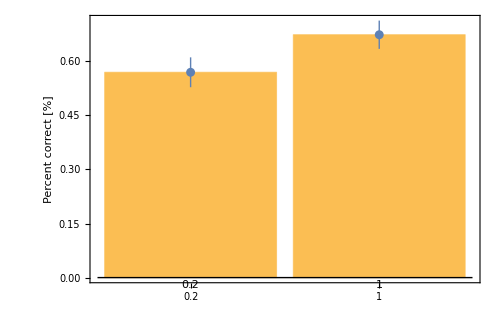

```mathematica
(Show[BarChart[#[[;;,1,2]],Frame-> {False,True,False,False},Axes->{True,False},BaseStyle->Directive[FontSize->20],FrameLabel->{None,"Percent correct [%]"},FrameStyle->20,ChartLabels->{"0.2","1"},ImageSize->500],ErrorListPlot[{#[[;;,1,2]],#[[;;,2,1]]}ᵀ,PlotRange->{{0,1}},Frame-> {True,True,False,False},PlotStyle->Thick]])&@({{ToExpression@#[[1,1]],N@Mean[#[[;;,2]]]},ErrorBar[N@(StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]]))]}&/@
SortBy[(GatherBy[Join@@Map[{N@#[[2]],N@#[[-1]]}&,DataCleanAllGraded,{2}],First]),First])
```

```mathematica
MannWhitneyTest@(GatherBy[Join@@Map[{N@#[[2]],N@#[[-1]]}&,DataCleanAllGraded,{2}],First][[;;,;;,2]])
```

0.0687449

### Percent correct vs. Angle Size

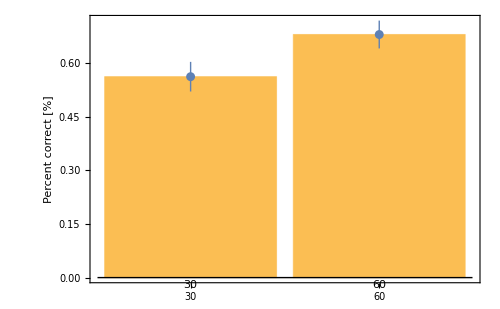

```mathematica
(Show[BarChart[#[[;;,1,2]],Frame-> {False,True,False,False},Axes->{True,False},BaseStyle->Directive[FontSize->20],FrameLabel->{None,"Percent correct [%]"},FrameStyle->20,ChartLabels->{"30","60"},ImageSize->500],ErrorListPlot[{#[[;;,1,2]],#[[;;,2,1]]}ᵀ,PlotRange->{{0,1}},Frame-> {True,True,False,False},PlotStyle->Thick]])&@({{ToExpression@#[[1,1]],N@Mean[#[[;;,2]]]},ErrorBar[N@(StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]]))]}&/@
SortBy[(GatherBy[Join@@Map[{N@#[[1]],N@#[[-1]]}&,DataCleanAllGraded,{2}],First]),First])
```

```mathematica
MannWhitneyTest@(GatherBy[Join@@Map[{N@#[[1]],N@#[[-1]]}&,DataCleanAllGraded,{2}],First][[;;,;;,2]])
```

0.039145

### Percent correct vs. Side length

```mathematica
(*1=angle; 2=base factor; 3=Qtype; 4=Manipulation; 5=What's manipulated; 6=correct answer; 7=timing; 8=user answer; 9=correct/not*)
```

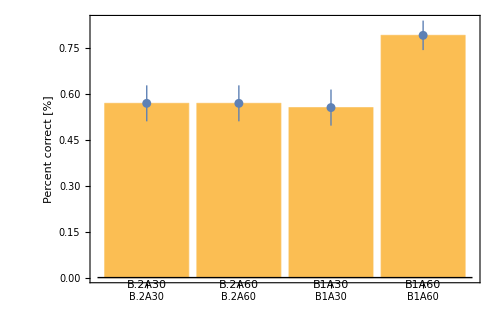

```mathematica
(Show[BarChart[#[[;;,1,2]],Frame-> {False,True,False,False},Axes->{True,False},BaseStyle->Directive[FontSize->20],FrameLabel->{None,"Percent correct [%]"},FrameStyle->20,ChartLabels->{"B.2A30","B.2A60","B1A30","B1A60"},ImageSize->500],ErrorListPlot[{#[[;;,1,2]],#[[;;,2,1]]}ᵀ,PlotRange->{{0,1}},Frame-> {True,True,False,False},PlotStyle->Thick]])&@({{#[[1,1]],Mean[#[[;;,2]]]},ErrorBar[N@(StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]]))]}&/@SortBy[GatherBy[Join@@Map[{N@((ToExpression@#[[2]])/Cos[ToExpression@#[[1]] Degree]),N@#[[-1]]}&,DataCleanAllGraded,{2}],First],First])
```

### Percent correct vs. Question type

```mathematica
(*1=angle; 2=base factor; 3=Qtype; 4=Manipulation; 5=What's manipulated; 6=correct answer; 7=timing; 8=user answer; 9=correct/not*)
```

#### What’s being asked about (people get better vertex location than angle estimations)

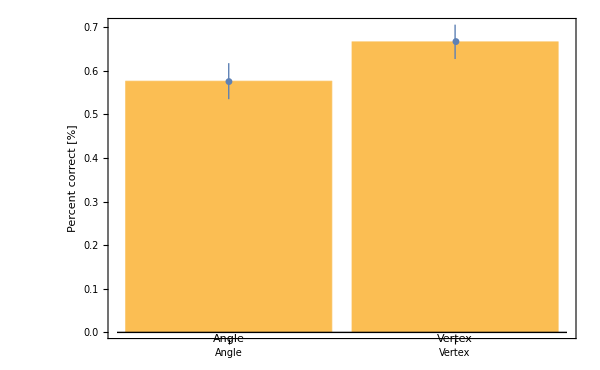

```mathematica
Show[BarChart[#[[;;,1,2]],ChartLabels->{"Angle","Vertex"},Frame-> {False,True,False,False}
 ,Axes->{True,False},BaseStyle->Directive[FontSize->16],FrameLabel->{None,"Percent correct [%]"},FrameStyle->18,ImageSize->600],ErrorListPlot[#,Frame-> {True,True,False,False},FrameLabel->{"QuestionType [angle/vertex]","Percent answers correct"},PlotStyle->Thick,PlotMarkers->Automatic]]&@SortBy[Join[{{#[[1,1]],N@Mean[#[[;;,2]]]},N@ErrorBar[StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]])]}&/@(GatherBy[Join@@Map[{If[#[[3]]=="angle",1,2],N@#[[-1]]}&,DataCleanAllGraded,{2}],First])],First]
```

```mathematica
MannWhitneyTest@(GatherBy[Join@@Map[{If[#[[3]]=="angle",1,2],N@#[[-1]]}&,DataCleanAllGraded,{2}],First][[;;,;;,2]])
```

0.114675

#### What’s being manipulated (angle manipulation easier than distance manipulations)

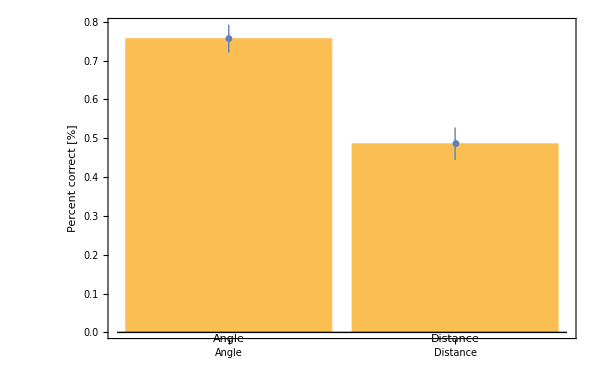

```mathematica
Show[BarChart[#[[;;,1,2]],ChartLabels->{"Angle","Distance"},Frame-> {False,True,False,False}
 ,Axes->{True,False},BaseStyle->Directive[FontSize->16],FrameLabel->{None,"Percent correct [%]"},FrameStyle->18,ImageSize->600],ErrorListPlot[#,Frame-> {True,True,False,False},FrameLabel->{"QuestionType [angle/vertex]","Percent answers correct"},PlotStyle->Thick,PlotMarkers->Automatic]]&@SortBy[Join[{{#[[1,1]],N@Mean[#[[;;,2]]]},N@ErrorBar[StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]])]}&/@(GatherBy[Join@@Map[{If[#[[5]]=="angle",1,2],N@#[[-1]]}&,DataCleanAllGraded,{2}],First])],First]
```

```mathematica
MannWhitneyTest@((GatherBy[Join@@Map[{If[#[[5]]=="angle",1,2],N@#[[-1]]}&,DataCleanAllGraded,{2}],First])[[;;,;;,2]])
```

2.25397×10^-6

#### What’s being manipulated (no difference for increase/decrease)

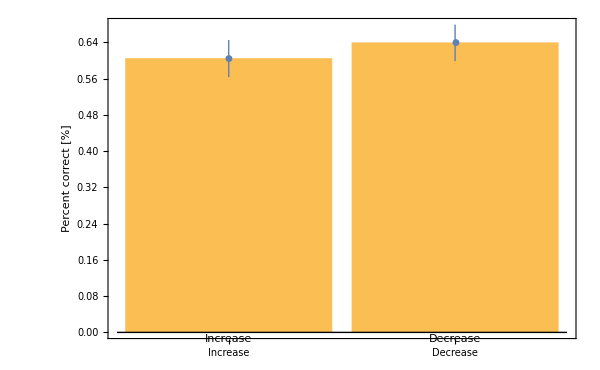

```mathematica
Show[BarChart[#[[;;,1,2]],ChartLabels->{"Increase","Decrease"},Frame-> {False,True,False,False}
 ,Axes->{True,False},BaseStyle->Directive[FontSize->16],FrameLabel->{None,"Percent correct [%]"},FrameStyle->18,ImageSize->600],ErrorListPlot[#,Frame-> {True,True,False,False},FrameLabel->{"QuestionType [angle/vertex]","Percent answers correct"},PlotStyle->Thick,PlotMarkers->Automatic]]&@SortBy[Join[{{#[[1,1]],N@Mean[#[[;;,2]]]},N@ErrorBar[StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]])]}&/@(GatherBy[Join@@Map[{If[#[[4]]=="increase",1,2],N@#[[-1]]}&,DataCleanAllGraded,{2}],First])],First]
```

```mathematica
MannWhitneyTest@(SortBy[GatherBy[Join@@Map[{If[#[[4]]=="increase",1,2],N@#[[-1]]}&,DataCleanAllGraded,{2}],First],First][[;;,;;,2]])
```

0.543679

#### Every Question Type Alone (easiest -> vertex and angle change, hardest->angles when distance changes)

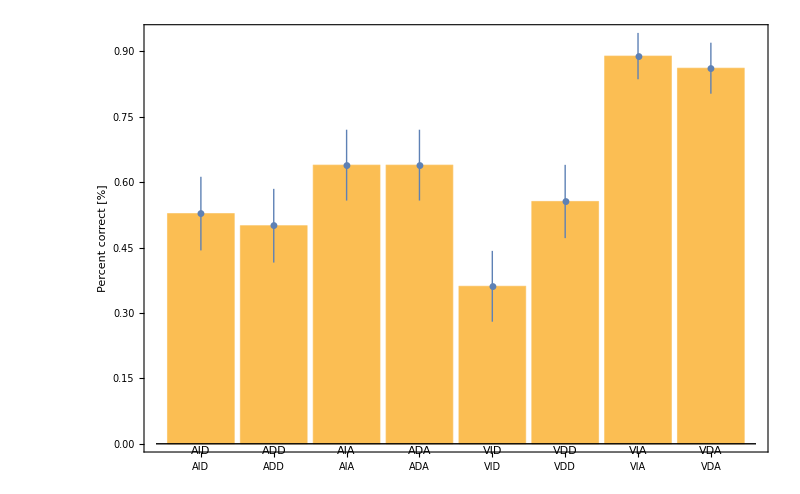

```mathematica
Show[BarChart[#[[;;,1,2]],Frame-> {False,True,False,False}
 ,Axes->{True,False},BaseStyle->Directive[FontSize->20]
 ,FrameLabel->{None,"Percent correct [%]"},FrameStyle->20,ChartLabels->{"AID","ADD","AIA","ADA","VID","VDD","VIA","VDA"},ImageSize->800],ErrorListPlot[#,Frame-> {True,True,False,False},FrameLabel->{"QuestionType [angle/vertex]","Percent answers correct"},PlotStyle->Thick,PlotMarkers->Automatic]]&@SortBy[Join[{{#[[1,1]],N@Mean[#[[;;,2]]]},N@ErrorBar[StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]])]}&/@(GatherBy[Join@@Map[{#[[{3,4,5}]],N@#[[-1]]}&,DataCleanAllGraded,{2}]/.rules,First])],First]
```

```mathematica
AnswerRules={"downward"-> 1,"stayPlace"-> 2,"upward"-> 3,"smaller"-> 1,"same"-> 2,"bigger"-> 3};
```

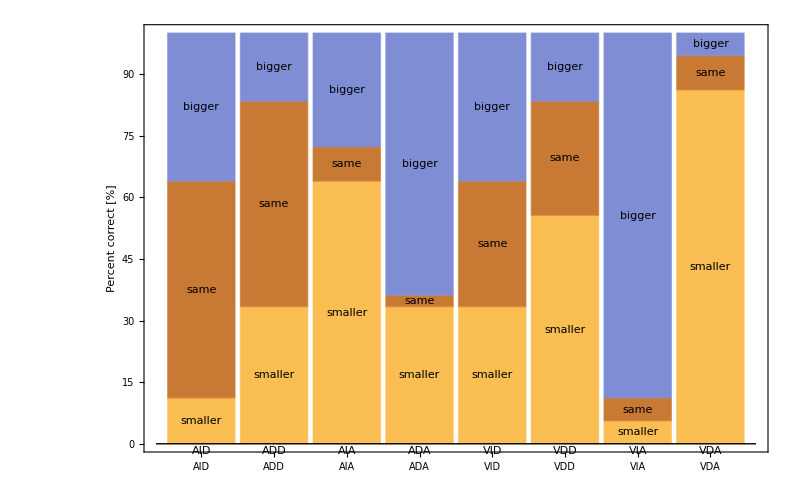

```mathematica
BarChart[#[[;;,2]],ChartLayout->"Percentile",ChartLabels->{{"AID","ADD","AIA","ADA","VID","VDD","VIA","VDA"},{"smaller","same","bigger"}},Frame-> {False,True,False,False},Axes->{True,False},BaseStyle->Directive[FontSize->18]
 ,FrameLabel->{None,"Percent correct [%]"},FrameStyle->20,ImageSize->800]&@SortBy[{#[[1,1]],SortBy[Tally[#[[;;,2]]],First][[;;,2]]}&/@(GatherBy[Join@@Map[{#[[{3,4,5}]],#[[8]]/.AnswerRules}&,DataCleanAllGraded,{2}]/.rules,First]),First]
```

## Response times

### Response times vs. Base length (perhaps a slight dependence on base length)

```mathematica
(*1=angle; 2=base factor; 3=Qtype; 4=Manipulation; 5=What's manipulated; 6=correct answer; 7=timing; 8=user answer; 9=correct/not*)
```

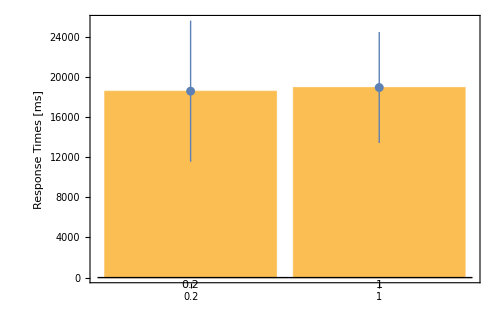

```mathematica
(Show[BarChart[#[[;;,1,2]],Frame-> {False,True,False,False},Axes->{True,False},BaseStyle->Directive[FontSize->20],FrameLabel->{None,"Response Times [ms]"},FrameStyle->20,ChartLabels->{"0.2","1"},ImageSize->500],ErrorListPlot[{#[[;;,1,2]],#[[;;,2,1]]}ᵀ,PlotRange->{{0,1}},Frame-> {True,True,False,False},PlotStyle->Thick]])&@({{ToExpression@#[[1,1]],N@Mean[#[[;;,2]]]},ErrorBar[N@MedianDeviation[#[[;;,2]]]]}&/@
GatherBy[Join@@Map[{N@#[[2]],N@ToExpression@#[[7]]}&,DataCleanAllGraded,{2}],First])
```

### Response Times vs. Angle Size (mean - slight angle size dependence, median - no dependence on angle size)

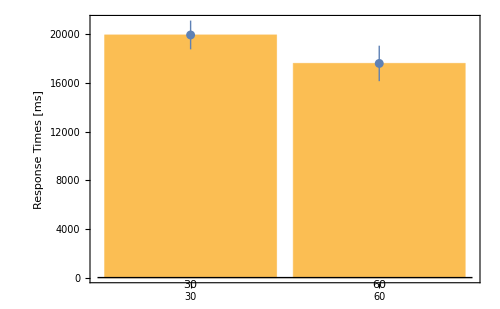

```mathematica
(Show[BarChart[#[[;;,1,2]],Frame-> {False,True,False,False},Axes->{True,False},BaseStyle->Directive[FontSize->20],FrameLabel->{None,"Response Times [ms]"},FrameStyle->20,ChartLabels->{"30","60"},ImageSize->500],ErrorListPlot[{#[[;;,1,2]],#[[;;,2,1]]}ᵀ,PlotRange->{{0,1}},Frame-> {True,True,False,False},PlotStyle->Thick]])&@({{ToExpression@#[[1,1]],N@Mean[#[[;;,2]]]},ErrorBar[N@(StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]]))]}&/@
SortBy[GatherBy[Join@@Map[{N@#[[1]],N@ToExpression@#[[7]]}&,DataCleanAllGraded,{2}],First],First])
```

```mathematica
MannWhitneyTest[SortBy[GatherBy[Join@@Map[{N@#[[1]],N@ToExpression@#[[7]]}&,DataCleanAllGraded,{2}],First],First][[;;,;;,2]]]
```

0.0300056

### Response Time vs. Side length

```mathematica
(*1=angle; 2=base factor; 3=Qtype; 4=Manipulation; 5=What's manipulated; 6=correct answer; 7=timing; 8=user answer; 9=correct/not*)
```

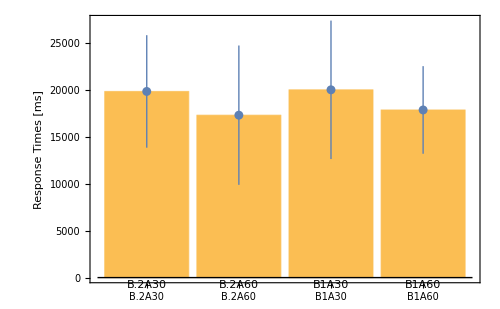

```mathematica
(Show[BarChart[#[[;;,1,2]],Frame-> {False,True,False,False},Axes->{True,False},BaseStyle->Directive[FontSize->20],FrameLabel->{None,"Response Times [ms]"},FrameStyle->20,ChartLabels->{"B.2A30","B.2A60","B1A30","B1A60"},ImageSize->500],ErrorListPlot[{#[[;;,1,2]],#[[;;,2,1]]}ᵀ,PlotRange->{{0,1}},Frame-> {True,True,False,False},PlotStyle->Thick]])&@SortBy[({{#[[1,1]],Mean[#[[;;,2]]]},ErrorBar[N@MedianDeviation[#[[;;,2]]]]}&/@GatherBy[Join@@Map[{N@((ToExpression@#[[2]])/Cos[ToExpression@#[[1]] Degree]),N@ToExpression@#[[7]]}&,DataCleanAllGraded,{2}],First]),First]
```

### Response Time vs. Question type

```mathematica
(*1=angle; 2=base factor; 3=Qtype; 4=Manipulation; 5=What's manipulated; 6=correct answer; 7=timing; 8=user answer; 9=correct/not*)
```

#### What’s being asked about (no difference)

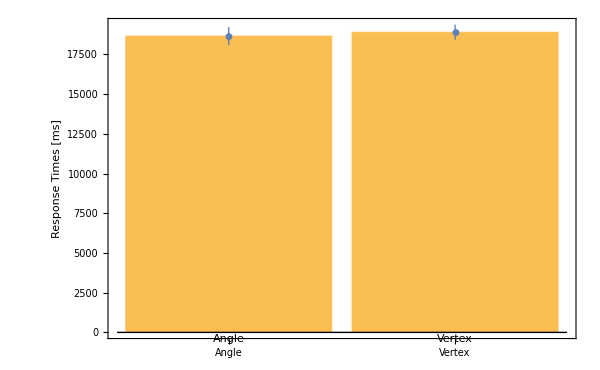

```mathematica
Show[BarChart[#[[;;,1,2]],ChartLabels->{"Angle","Vertex"},Frame-> {False,True,False,False}
 ,Axes->{True,False},BaseStyle->Directive[FontSize->16],FrameLabel->{None,"Response Times [ms]"},FrameStyle->18,ImageSize->600],ErrorListPlot[#,Frame-> {True,True,False,False},FrameLabel->{"QuestionType [angle/vertex]","Percent answers correct"},PlotStyle->Thick,PlotMarkers->Automatic]]&@SortBy[Join[{{#[[1,1]],N@Mean[#[[;;,2]]]},N@ErrorBar[MedianDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]])]}&/@(GatherBy[Join@@Map[{If[#[[3]]=="angle",1,2],N@ToExpression@#[[7]]}&,DataCleanAllGraded,{2}],First])],First]
```

```mathematica
MannWhitneyTest@(GatherBy[Join@@Map[{If[#[[3]]=="angle",1,2],N@ToExpression@#[[7]]}&,DataCleanAllGraded,{2}],First])[[;;,;;,2]]
```

0.214598

#### What’s being manipulated (no difference between changes of angle and changes of distance)

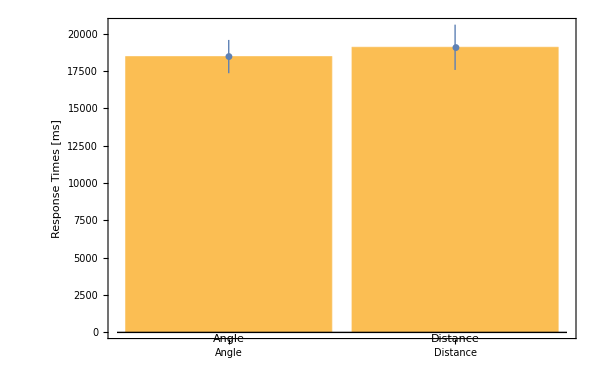

```mathematica
Show[BarChart[#[[;;,1,2]],ChartLabels->{"Angle","Distance"},Frame-> {False,True,False,False}
 ,Axes->{True,False},BaseStyle->Directive[FontSize->18],FrameLabel->{None,"Response Times [ms]"},FrameStyle->20,ImageSize->600],ErrorListPlot[#,Frame-> {True,True,False,False},FrameLabel->{"QuestionType [angle/vertex]","Response Times"},PlotStyle->Thick,PlotMarkers->Automatic]]&@SortBy[Join[{{#[[1,1]],N@Mean[#[[;;,2]]]},N@ErrorBar[StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]])]}&/@(GatherBy[Join@@Map[{If[#[[5]]=="angle",1,2],N@ToExpression@#[[7]]}&,DataCleanAllGraded,{2}],First])],First]
```

```mathematica
MannWhitneyTest@(GatherBy[Join@@Map[{If[#[[5]]=="angle",1,2],N@ToExpression@#[[7]]}&,DataCleanAllGraded,{2}],First])[[;;,;;,2]]
```

0.771206

#### What’s the manipulation - Increase/Decrease

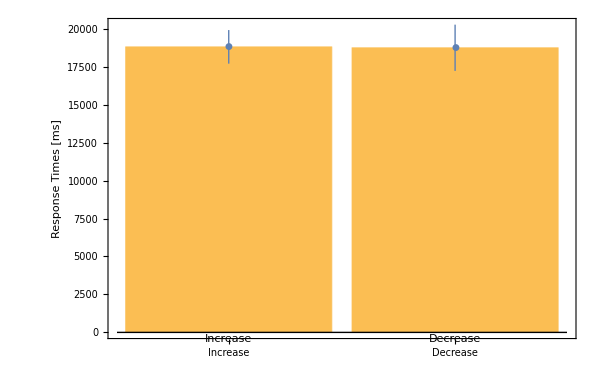

```mathematica
Show[BarChart[#[[;;,1,2]],ChartLabels->{"Increase","Decrease"},Frame-> {False,True,False,False}
 ,Axes->{True,False},BaseStyle->Directive[FontSize->18],FrameLabel->{None,"Response Times [ms]"},FrameStyle->20,ImageSize->600],ErrorListPlot[#,Frame-> {True,True,False,False},FrameLabel->{"QuestionType [angle/vertex]","Response Times"},PlotStyle->Thick,PlotMarkers->Automatic]]&@SortBy[Join[{{#[[1,1]],N@Mean[#[[;;,2]]]},N@ErrorBar[StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]])]}&/@(GatherBy[Join@@Map[{If[#[[4]]=="increase",1,2],N@ToExpression@#[[7]]}&,DataCleanAllGraded,{2}],First])],First]
```

```mathematica
MannWhitneyTest@(GatherBy[Join@@Map[{If[#[[4]]=="increase",1,2],N@ToExpression@#[[7]]}&,DataCleanAllGraded,{2}],First])[[;;,;;,2]]
```

0.162085

#### Every Question Type Alone

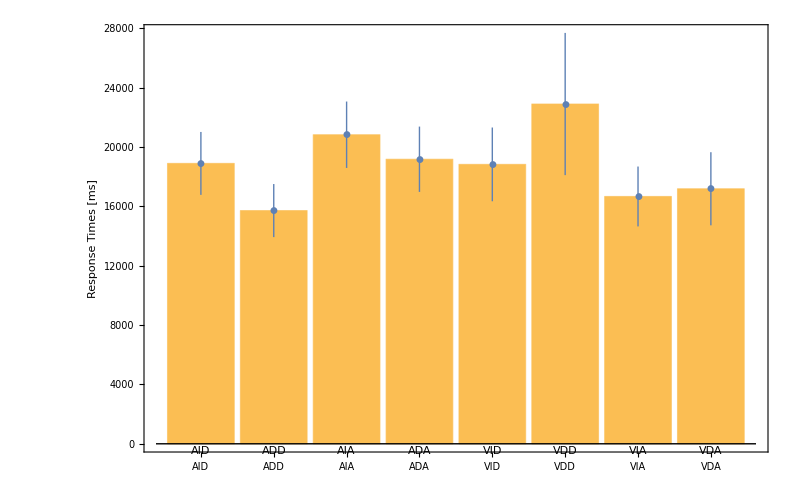

```mathematica
Show[BarChart[#[[;;,1,2]],Frame-> {False,True,False,False}
 ,Axes->{True,False},BaseStyle->Directive[FontSize->20],FrameLabel->{None,"Response Times [ms]"},FrameStyle->20,ChartLabels->{"AID","ADD","AIA","ADA","VID","VDD","VIA","VDA"},ImageSize->800],ErrorListPlot[#,Frame-> {True,True,False,False},PlotStyle->Thick,PlotMarkers->Automatic]]&@SortBy[Join[{{#[[1,1]],N@Mean[#[[;;,2]]]},N@ErrorBar[StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]]) ]}&/@(GatherBy[Join@@Map[{#[[{3,4,5}]],N@ToExpression@#[[7]]}&,DataCleanAllGraded,{2}]/.rules,First])],First]
```

```mathematica
MannWhitneyTest@(SortBy[(GatherBy[Join@@Map[{#[[{3,4,5}]],N@ToExpression@#[[7]]}&,DataCleanAllGraded,{2}]/.rules,First]),First][[{1,2},;;,2]])
```

0.189501

## Analysis per Question Type

```mathematica
(*1=angle; 2=base factor; 3=timing; 4=user answer; 5=correct/not*)
```

```mathematica
DataPerQTypeAll=(Sort@GatherBy[Join@@Map[{#[[3;;5]]/.rules,#[[{1,2,7,8,9}]]}&,DataCleanAllGraded,{2}],First])[[;;,;;,2]];
```

### Percent correct vs. Base length

```mathematica
(*1=angle; 2=base factor; 3=timing; 4=user answer; 5=correct/not*)
```

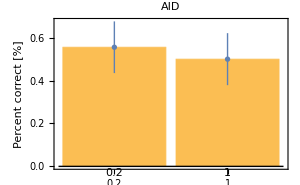
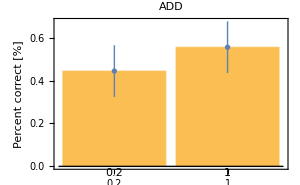
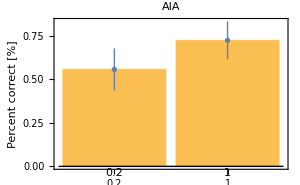
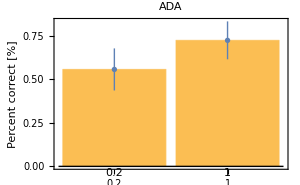
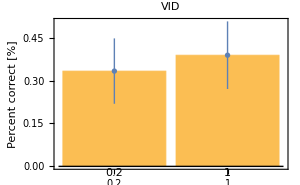
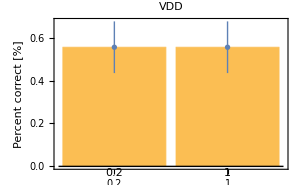
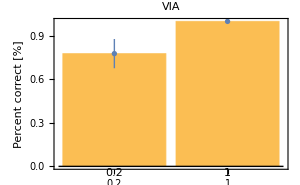
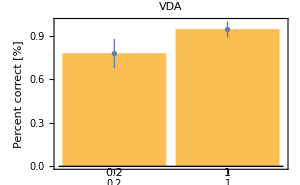

```mathematica
MapIndexed[(Show[BarChart[#[[;;,1,2]],PlotLabel->QuestionType[[#2[[1]]]],Frame-> {False,True,False,False},Axes->{True,False},BaseStyle->Directive[FontSize->16],FrameLabel->{None,"Percent correct [%]"},FrameStyle->16,ChartLabels->{"0.2","1"},ImageSize->300],ErrorListPlot[{#[[;;,1,2]],#[[;;,2,1]]}ᵀ,PlotRange->{{0,1}},Frame-> {True,True,False,False},PlotStyle->Thick]])&,(SortBy[#,First]&/@Map[{{ToExpression@#[[1,1]],N@Mean[#[[;;,2]]]},ErrorBar[N@(StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]]))]}&,(GatherBy[#,First]&/@Map[{N@#[[2]],N@#[[-1]]}&,DataPerQTypeAll,{2}]),{2}]),{1}]
```

```mathematica
Manipulate[(Show[BarChart[Evaluate@#[[;;,;;,1,2]],PlotLabel->QuestionType[[{i,j}]],PlotRange->{{PerLow,PerHigh}},Frame-> {False,True,False,False},Axes->{True,False},BaseStyle->Directive[FontSize->16],FrameLabel->{None,"Percent correct [%]"},FrameStyle->16,ChartLabels->{"0.2","1"},ImageSize->500],ErrorListPlot[{#[[;;,1,2]],#[[;;,2,1]]}ᵀ,PlotRange->{{PerLow,PerHigh}},Frame-> {True,True,False,False},PlotStyle->Thick]])&@(SortBy[#,First]&/@Map[{{ToExpression@#[[1,1]],N@Mean[#[[;;,2]]]},ErrorBar[N@(StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]]))]}&,(GatherBy[#,First]&/@Map[{N@#[[2]],N@#[[-1]]}&,DataPerQTypeAll,{2}]),{2}])[[{i,j}]],{{i,1},1,8,1},{{j,2},1,8,1},{{PerLow,0},0,1},{{PerHigh,0.8},0.4,1}]
```

### Percent correct vs. Angle Size

```mathematica
(*1=angle; 2=base factor; 3=timing; 4=user answer; 5=correct/not*)
```

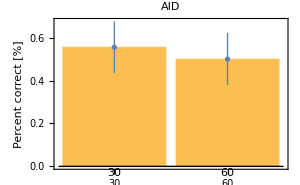
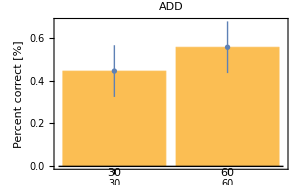
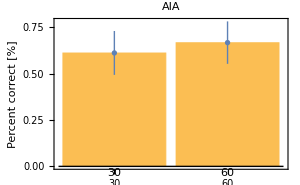
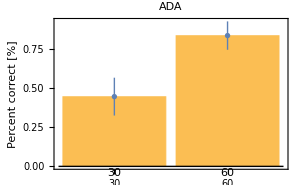
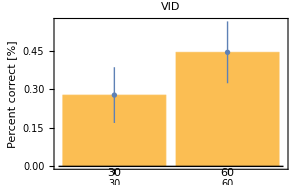
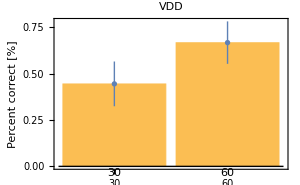
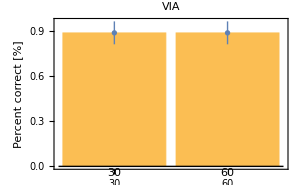
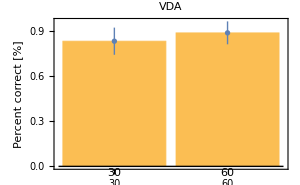

```mathematica
MapIndexed[(Show[BarChart[#[[;;,1,2]],PlotLabel->QuestionType[[#2[[1]]]],Frame-> {False,True,False,False},Axes->{True,False},BaseStyle->Directive[FontSize->16],FrameLabel->{None,"Percent correct [%]"},FrameStyle->16,ChartLabels->{"30","60"},ImageSize->300],ErrorListPlot[{#[[;;,1,2]],#[[;;,2,1]]}ᵀ,PlotRange->{{0,1}},Frame-> {True,True,False,False},PlotStyle->Thick]])&,(SortBy[#,First]&/@Map[{{ToExpression@#[[1,1]],N@Mean[#[[;;,2]]]},ErrorBar[N@(StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]]))]}&,(GatherBy[#,First]&/@Map[{N@#[[1]],N@#[[-1]]}&,DataPerQTypeAll,{2}]),{2}]),{1}]
```

```mathematica
Manipulate[ErrorListPlot[Evaluate@#,PlotRange->{{0,90},{PerLow,PerHigh}},PlotLabel->QuestionType[[{i,j}]], Frame-> {True,True,False,False},FrameLabel->{"Angle Size [deg]","% correct"},PlotStyle->Thick,PlotMarkers->Automatic,FrameStyle->16,ImageSize->330]&@(SortBy[#,First]&/@Map[{{ToExpression@#[[1,1]],N@Mean[#[[;;,2]]]},ErrorBar[N@(StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]]))]}&,(GatherBy[#,First]&/@Map[{N@#[[1]],N@#[[-1]]}&,DataPerQTypeAll,{2}]),{2}])[[{i,j}]],{{i,1},1,8,1},{{j,2},1,8,1},{{PerLow,0.3},0.2,1},{{PerHigh,0.8},0.4,1}]
```

### Response times vs. Base length

```mathematica
(*1=angle; 2=base factor; 3=timing; 4=user answer; 5=correct/not*)
```

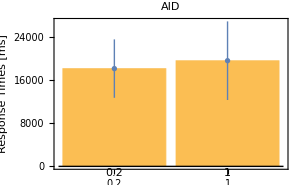
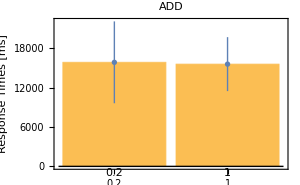
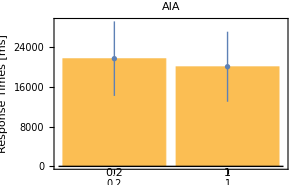
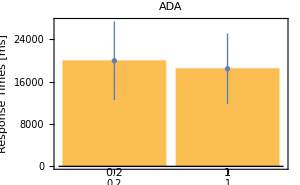
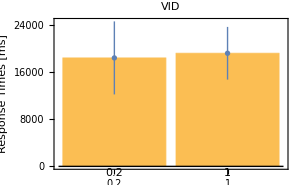
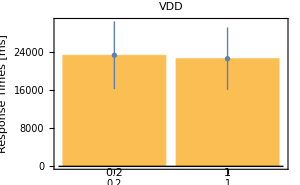
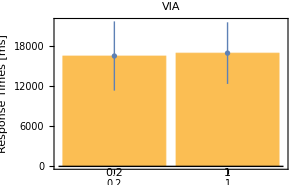
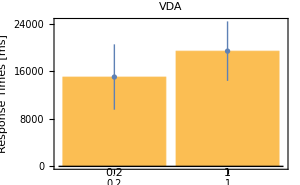

```mathematica
MapIndexed[(Show[BarChart[#1[[;;,1,2]],PlotLabel->QuestionType[[#2[[1]]]],Frame-> {False,True,False,False},Axes->{True,False},BaseStyle->Directive[FontSize->16],FrameLabel->{None,"Response Times [ms]"},FrameStyle->16,ChartLabels->{"0.2","1"},ImageSize->300],ErrorListPlot[{#[[;;,1,2]],#[[;;,2,1]]}ᵀ,PlotRange->{{0,1}},Frame-> {True,True,False,False},PlotStyle->Thick]])&,(SortBy[#,First]&/@Map[{{ToExpression@#[[1,1]],N@Mean[#[[;;,2]]]},ErrorBar[N@MedianDeviation[#[[;;,2]]]]}&,(GatherBy[#,First]&/@Map[{N@#[[2]],N@ToExpression@#[[3]]}&,DataPerQTypeAll,{2}]),{2}]),{1}]
```

```mathematica
Manipulate[ErrorListPlot[#,PlotRange->{{0,1.1},{PerLow 10^3,PerHigh 10^3}},PlotLabel->QuestionType[[{i,j}]], Frame-> {True,True,False,False},FrameLabel->{"Base Length","Response Times [ms]"},PlotStyle->Thick,PlotMarkers->Automatic,FrameStyle->16,ImageSize->330]&@(SortBy[#,First]&/@Map[{{ToExpression@#[[1,1]],N@f[#[[;;,2]]]},ErrorBar[N@MedianDeviation@#[[;;,2]]]}&,(GatherBy[#,First]&/@Map[{N@#[[2]],N@ToExpression@#[[3]]}&,DataPerQTypeAll,{2}]),{2}])[[{i,j}]],{{i,1},1,8,1},{{j,2},1,8,1},{{PerLow,2},1,6},{{PerHigh,30},8,40},{f,{Median,Mean}}]
```

### Response times vs. Angle Size

```mathematica
(*1=angle; 2=base factor; 3=timing; 4=user answer; 5=correct/not*)
```

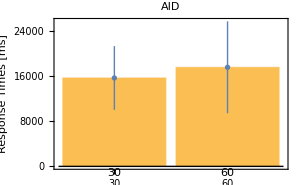
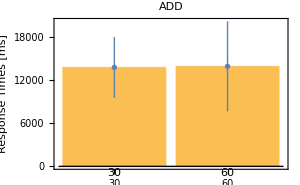
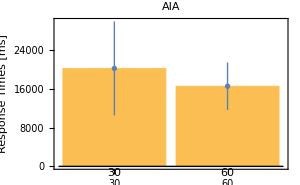
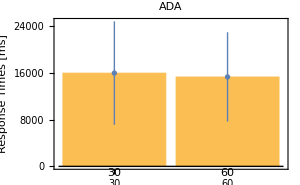
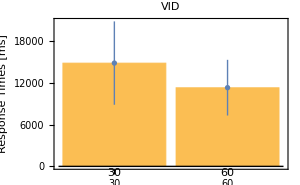
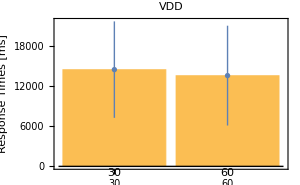
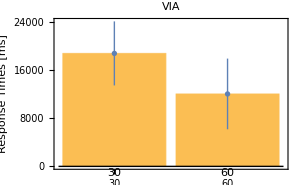
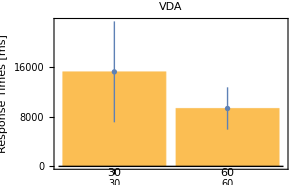

```mathematica
MapIndexed[(Show[BarChart[#1[[;;,1,2]],PlotLabel->QuestionType[[#2[[1]]]],Frame-> {False,True,False,False},Axes->{True,False},BaseStyle->Directive[FontSize->16],FrameLabel->{None,"Response Times [ms]"},FrameStyle->16,ChartLabels->{"30","60"},ImageSize->300],ErrorListPlot[{#[[;;,1,2]],#[[;;,2,1]]}ᵀ,PlotRange->{{0,1}},Frame-> {True,True,False,False},PlotStyle->Thick]])&,(SortBy[#,First]&/@Map[{{ToExpression@#[[1,1]],N@Median[#[[;;,2]]]},ErrorBar[N@MedianDeviation[#[[;;,2]]]]}&,(GatherBy[#,First]&/@Map[{N@#[[1]],N@ToExpression@#[[3]]}&,DataPerQTypeAll,{2}]),{2}]),{1}]
```

```mathematica
Manipulate[ErrorListPlot[#,PlotRange->{{0,90},{PerLow 10^3,PerHigh 10^3}},PlotLabel->QuestionType[[{i,j}]], Frame-> {True,True,False,False},FrameLabel->{"Angle Size","Response Times [ms]"},PlotStyle->Thick,PlotMarkers->Automatic,FrameStyle->16,ImageSize->600]&@(SortBy[#,First]&/@Map[{{ToExpression@#[[1,1]],N@f[#[[;;,2]]]},ErrorBar[N@MedianDeviation@#[[;;,2]]]}&,(GatherBy[#,First]&/@Map[{N@#[[1]],N@ToExpression@#[[3]]}&,DataPerQTypeAll,{2}]),{2}])[[{i,j}]],{{i,1},1,8,1},{{j,2},1,8,1},{{PerLow,2},1,6},{{PerHigh,30},8,40},{f,{Median,Mean}}]
```

Experts vs. Leute

```mathematica
ExpTH=0.8;
DataCleanAllGradedExperts=Select[DataCleanAllGraded,Mean[#[[;;,-1]]]>ExpTH&];
DataCleanAllGradedNonExperts=Select[DataCleanAllGraded,Mean[#[[;;,-1]]]≤ ExpTH&];
```

```mathematica
DataCleanAllGradedNonExperts//Dimensions
```

{28,8,9}

## Percent Correct

### Percent correct vs. Base length

```mathematica
(*1=angle; 2=base factor; 3=Qtype; 4=Manipulation; 5=What's manipulated; 6=correct answer; 7=timing; 8=user answer; 9=correct/not*)
```

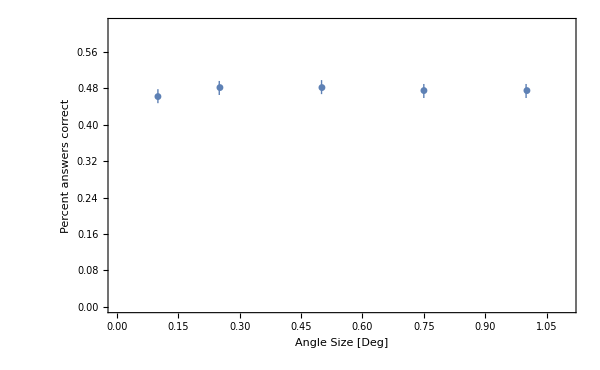

```mathematica
ErrorListPlot[#,PlotRange->{{0,1.1},{0,0.62}},Frame-> {True,True,False,False},FrameLabel->{"Angle Size [Deg]","Percent answers correct"},PlotStyle->Thick,PlotMarkers->Automatic,FrameStyle->20,ImageSize->600]&@({{ToExpression@#[[1,1]],N@Mean[#[[;;,2]]]},ErrorBar[N@(StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]]))]}&/@
GatherBy[Join@@Map[{N@#[[2]],N@#[[-1]]}&,DataCleanAllGradedNonExperts,{2}],First])
```

### Percent correct vs. Angle Size

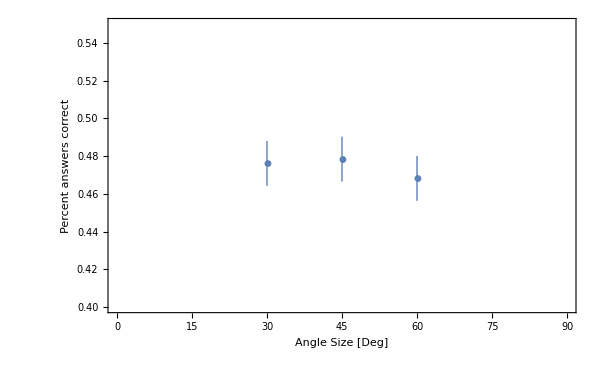

```mathematica
ErrorListPlot[#,PlotRange->{{0,90},{0.4,0.55}},Frame-> {True,True,False,False},FrameLabel->{"Angle Size [Deg]","Percent answers correct"},PlotStyle->Thick,PlotMarkers->Automatic,FrameStyle->20,ImageSize->600]&@({{ToExpression@#[[1,1]],N@Mean[#[[;;,2]]]},ErrorBar[N@(StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]]))]}&/@
GatherBy[Join@@Map[{N@#[[1]],N@#[[-1]]}&,DataCleanAllGradedNonExperts,{2}],First])
```

### Percent correct vs. Side length

```mathematica
(*1=angle; 2=base factor; 3=Qtype; 4=Manipulation; 5=What's manipulated; 6=correct answer; 7=timing; 8=user answer; 9=correct/not*)
```

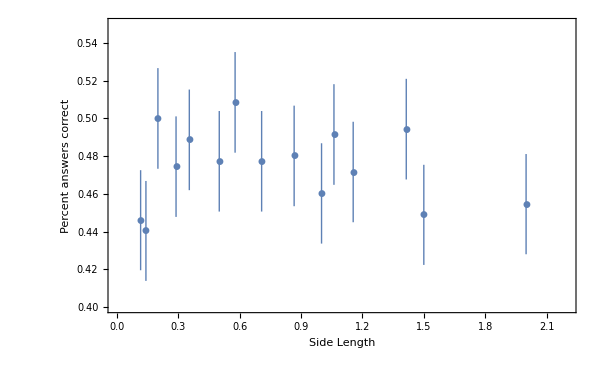

```mathematica
ErrorListPlot[#,(*Joined->True,*)PlotRange->{{0,2.2},{0.4,0.55}},Frame-> {True,True,False,False},FrameLabel->{"Side Length","Percent answers correct"},PlotStyle->Thick,PlotMarkers->Automatic,FrameStyle->20,ImageSize->600]&@({{#[[1,1]],Mean[#[[;;,2]]]},ErrorBar[N@(StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]]))]}&/@GatherBy[Join@@Map[{N@((ToExpression@#[[2]])/Cos[ToExpression@#[[1]] Degree]),N@#[[-1]]}&,DataCleanAllGradedNonExperts,{2}],First])
```

### Percent correct vs. Question type

```mathematica
(*1=angle; 2=base factor; 3=Qtype; 4=Manipulation; 5=What's manipulated; 6=correct answer; 7=timing; 8=user answer; 9=correct/not*)
```

#### What’s being asked about (people get better vertex location than angle estimations)

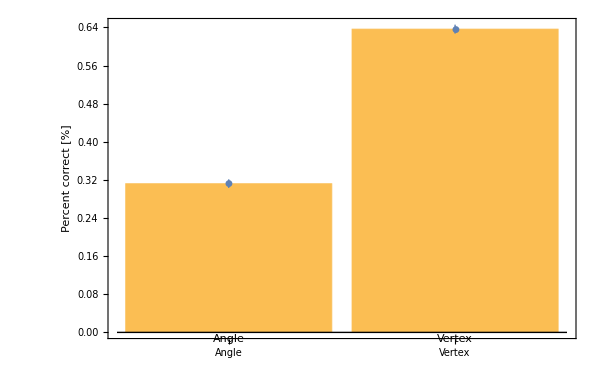

```mathematica
Show[BarChart[#[[;;,1,2]],ChartLabels->{"Angle","Vertex"},Frame-> {False,True,False,False}
 ,Axes->{True,False},BaseStyle->Directive[FontSize->16],FrameLabel->{None,"Percent correct [%]"},FrameStyle->18,ImageSize->600],ErrorListPlot[#,Frame-> {True,True,False,False},FrameLabel->{"QuestionType [angle/vertex]","Percent answers correct"},PlotStyle->Thick,PlotMarkers->Automatic]]&@SortBy[Join[{{#[[1,1]],N@Mean[#[[;;,2]]]},N@ErrorBar[StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]])]}&/@(GatherBy[Join@@Map[{If[#[[3]]=="angle",1,2],N@#[[-1]]}&,DataCleanAllGradedNonExperts,{2}],First])],First]
```

#### What’s being manipulated (angle manipulation easier than distance manipulations)

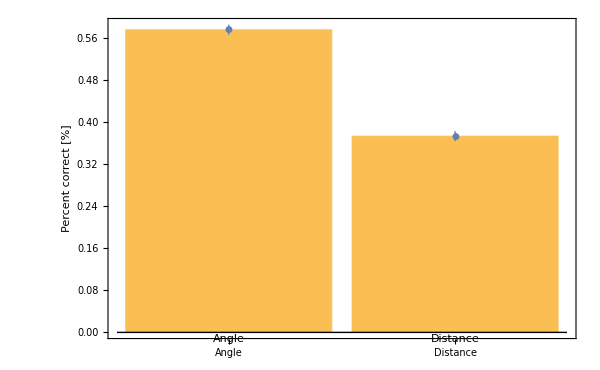

```mathematica
Show[BarChart[#[[;;,1,2]],ChartLabels->{"Angle","Distance"},Frame-> {False,True,False,False}
 ,Axes->{True,False},BaseStyle->Directive[FontSize->16],FrameLabel->{None,"Percent correct [%]"},FrameStyle->18,ImageSize->600],ErrorListPlot[#,Frame-> {True,True,False,False},FrameLabel->{"QuestionType [angle/vertex]","Percent answers correct"},PlotStyle->Thick,PlotMarkers->Automatic]]&@SortBy[Join[{{#[[1,1]],N@Mean[#[[;;,2]]]},N@ErrorBar[StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]])]}&/@(GatherBy[Join@@Map[{If[#[[5]]=="angle",1,2],N@#[[-1]]}&,DataCleanAllGradedNonExperts,{2}],First])],First]
```

#### What’s being manipulated (significant difference between increase and decrease!!!)

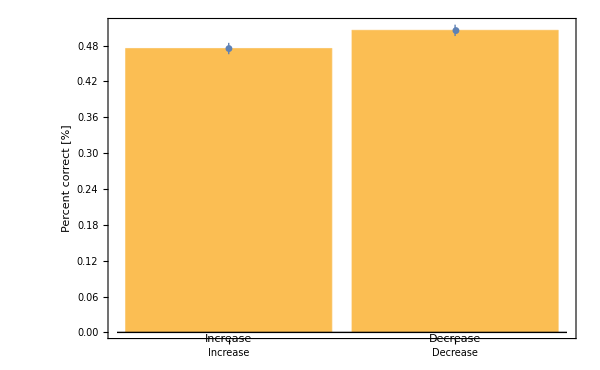

```mathematica
Show[BarChart[#[[;;,1,2]],ChartLabels->{"Increase","Decrease"},Frame-> {False,True,False,False}
 ,Axes->{True,False},BaseStyle->Directive[FontSize->16],FrameLabel->{None,"Percent correct [%]"},FrameStyle->18,ImageSize->600],ErrorListPlot[#,Frame-> {True,True,False,False},FrameLabel->{"QuestionType [angle/vertex]","Percent answers correct"},PlotStyle->Thick,PlotMarkers->Automatic]]&@SortBy[Join[{{#[[1,1]],N@Mean[#[[;;,2]]]},N@ErrorBar[StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]])]}&/@(GatherBy[Join@@Map[{If[#[[4]]=="increase",1,2],N@#[[-1]]}&,DataCleanAllGradedNonExperts,{2}],First])],First]
```

```mathematica
MannWhitneyTest@(GatherBy[Join@@Map[{If[#[[4]]=="increase",1,2],N@#[[-1]]}&,DataCleanAllGradedNonExperts,{2}],First][[;;,;;,2]])
```

0.0237319

#### Every Question Type Alone (easiest -> vertex and angle change, hardest->angles when distance changes)

```mathematica
rules={{"angle","increase","distance"}-> 1,{"angle","decrease","distance"}-> 2,{"angle","increase","angle"}-> 3,{"angle","decrease","angle"}->4,{"vertex","increase","distance"}->5,{"vertex","decrease","distance"}-> 6,{"vertex","increase","angle"}-> 7,{"vertex","decrease","angle"}-> 8};
```

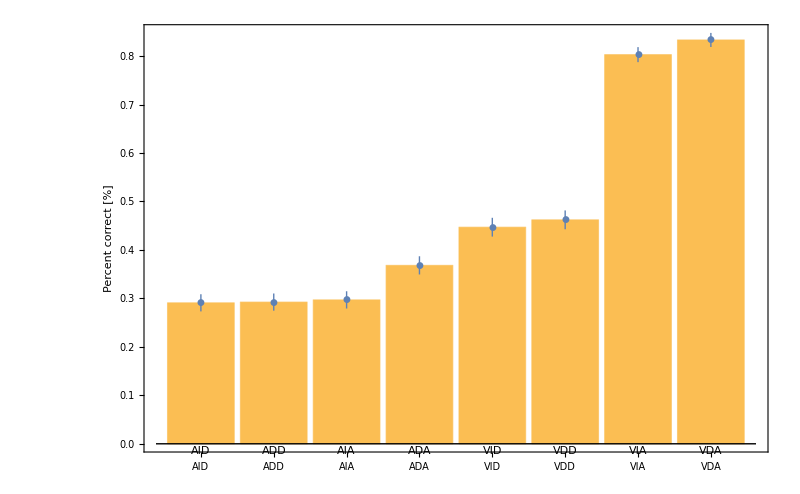

```mathematica
Show[BarChart[#[[;;,1,2]],Frame-> {False,True,False,False}
 ,Axes->{True,False},BaseStyle->Directive[FontSize->20]
 ,FrameLabel->{None,"Percent correct [%]"},FrameStyle->20,ChartLabels->{"AID","ADD","AIA","ADA","VID","VDD","VIA","VDA"},ImageSize->800],ErrorListPlot[#,Frame-> {True,True,False,False},FrameLabel->{"QuestionType [angle/vertex]","Percent answers correct"},PlotStyle->Thick,PlotMarkers->Automatic]]&@SortBy[Join[{{#[[1,1]],N@Mean[#[[;;,2]]]},N@ErrorBar[StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]])]}&/@(GatherBy[Join@@Map[{#[[{3,4,5}]],N@#[[-1]]}&,DataCleanAllGradedNonExperts,{2}]/.rules,First])],First]
```

```mathematica
AnswerRules={"downward"-> 1,"stayPlace"-> 2,"upward"-> 3,"smaller"-> 1,"same"-> 2,"bigger"-> 3};
```

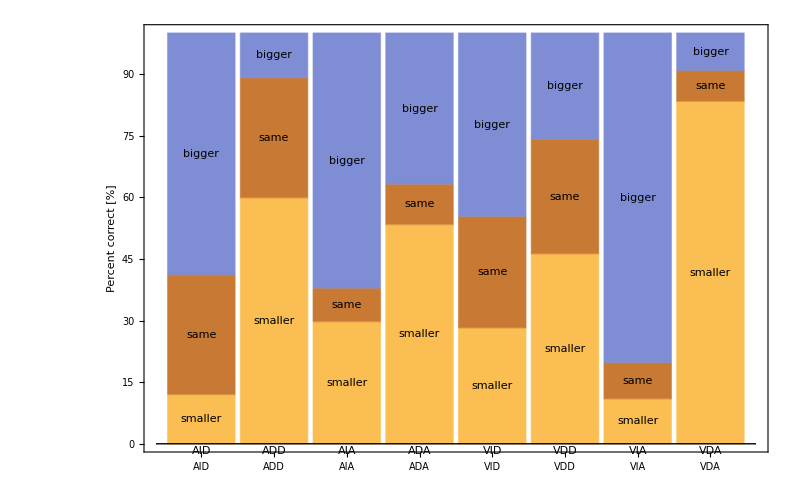

```mathematica
BarChart[#[[;;,2]],ChartLayout->"Percentile",ChartLabels->{{"AID","ADD","AIA","ADA","VID","VDD","VIA","VDA"},{"smaller","same","bigger"}},Frame-> {False,True,False,False},Axes->{True,False},BaseStyle->Directive[FontSize->18]
 ,FrameLabel->{None,"Percent correct [%]"},FrameStyle->20,ImageSize->800]&@SortBy[{#[[1,1]],SortBy[Tally[#[[;;,2]]],First][[;;,2]]}&/@(GatherBy[Join@@Map[{#[[{3,4,5}]],#[[8]]/.AnswerRules}&,DataCleanAllGradedNonExperts,{2}]/.rules,First]),First]
```

## Response times

### Response times vs. Base length (perhaps a slight dependence on base length)

```mathematica
(*1=angle; 2=base factor; 3=Qtype; 4=Manipulation; 5=What's manipulated; 6=correct answer; 7=timing; 8=user answer; 9=correct/not*)
```

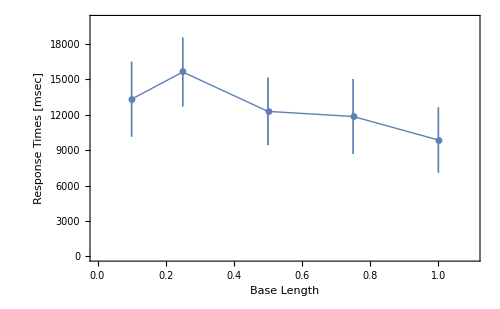

```mathematica
ErrorListPlot[#,Joined->True,PlotRange->{{0,1.1},{0,20 10^3}},Frame-> {True,True,False,False},FrameStyle-> 18,ImageSize-> 500,FrameLabel->{"Base Length","Response Times [msec]"},PlotStyle->Thick,PlotMarkers->Automatic]&@({{ToExpression@#[[1,1]],N@Mean[#[[;;,2]]]},ErrorBar[N@MedianDeviation[#[[;;,2]]]]}&/@
GatherBy[Join@@Map[{N@#[[2]],N@ToExpression@#[[7]]}&,DataCleanAllGradedNonExperts,{2}],First])
```

### Response Times vs. Angle Size (mean - slight angle size dependence, median - no dependence on angle size)

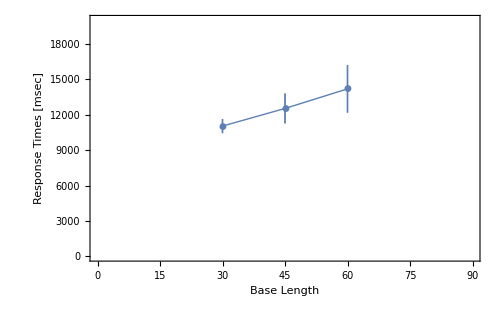

```mathematica
ErrorListPlot[#,Joined->True,PlotRange->{{0,90},{0,20 10^3}},Frame-> {True,True,False,False},FrameStyle-> 18,ImageSize-> 500,FrameLabel->{"Base Length","Response Times [msec]"},PlotStyle->Thick,PlotMarkers->Automatic]&@({{ToExpression@#[[1,1]],N@Mean[#[[;;,2]]]},ErrorBar[N@(StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]]))]}&/@
SortBy[GatherBy[Join@@Map[{N@#[[1]],N@ToExpression@#[[7]]}&,DataCleanAllGradedNonExperts,{2}],First],First])
```

```mathematica
MannWhitneyTest[SortBy[GatherBy[Join@@Map[{N@#[[1]],N@ToExpression@#[[7]]}&,DataCleanAllGradedNonExperts,{2}],First],First][[{1,3},;;,2]]]
```

0.284882

### Response Time vs. Side length

```mathematica
(*1=angle; 2=base factor; 3=Qtype; 4=Manipulation; 5=What's manipulated; 6=correct answer; 7=timing; 8=user answer; 9=correct/not*)
```

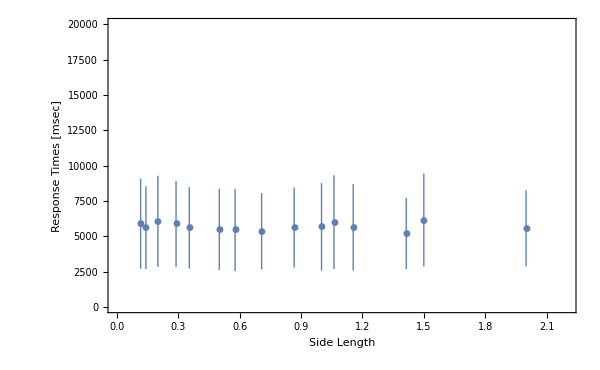

```mathematica
ErrorListPlot[#,(*Joined->True,*)PlotRange->{{0,2.2},{0,20 10^3}},Frame-> {True,True,False,False},FrameStyle-> 20,ImageSize-> 600,FrameLabel->{"Side Length","Response Times [msec]"},PlotStyle->Thick,PlotMarkers->Automatic]&@({{#[[1,1]],Median[#[[;;,2]]]},ErrorBar[N@MedianDeviation[#[[;;,2]]]]}&/@GatherBy[Join@@Map[{N@((ToExpression@#[[2]])/Cos[ToExpression@#[[1]] Degree]),N@ToExpression@#[[7]]}&,DataCleanAllGradedNonExperts,{2}],First])
```

### Response Time vs. Question type

```mathematica
(*1=angle; 2=base factor; 3=Qtype; 4=Manipulation; 5=What's manipulated; 6=correct answer; 7=timing; 8=user answer; 9=correct/not*)
```

#### What’s being asked about

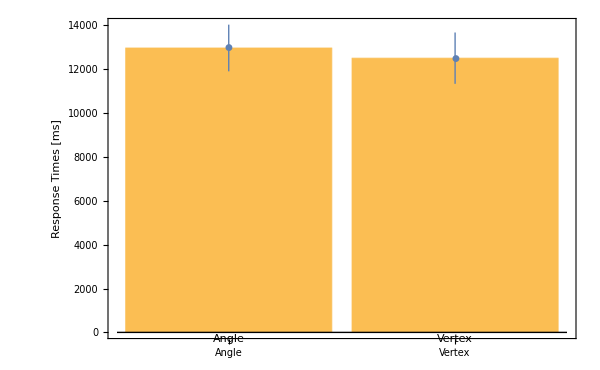

```mathematica
Show[BarChart[#[[;;,1,2]],ChartLabels->{"Angle","Vertex"},Frame-> {False,True,False,False}
 ,Axes->{True,False},BaseStyle->Directive[FontSize->16],FrameLabel->{None,"Response Times [ms]"},FrameStyle->18,ImageSize->600],ErrorListPlot[#,Frame-> {True,True,False,False},FrameLabel->{"QuestionType [angle/vertex]","Percent answers correct"},PlotStyle->Thick,PlotMarkers->Automatic]]&@SortBy[Join[{{#[[1,1]],N@Mean[#[[;;,2]]]},N@ErrorBar[StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]])]}&/@(GatherBy[Join@@Map[{If[#[[3]]=="angle",1,2],N@ToExpression@#[[7]]}&,DataCleanAllGradedNonExperts,{2}],First])],First]
```

```mathematica
MannWhitneyTest@(GatherBy[Join@@Map[{If[#[[3]]=="angle",1,2],N@ToExpression@#[[7]]}&,DataCleanAllGradedNonExperts,{2}],First])[[;;,;;,2]]
```

0.160393

#### What’s being manipulated

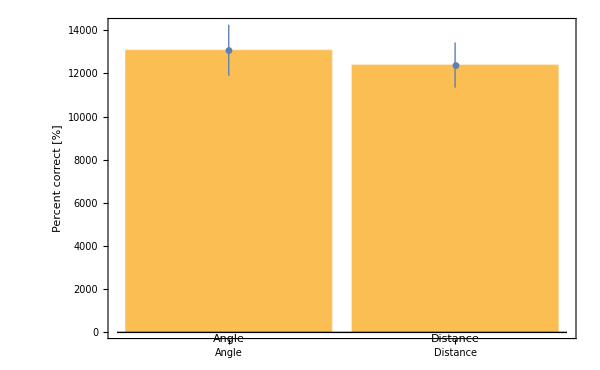

```mathematica
Show[BarChart[#[[;;,1,2]],ChartLabels->{"Angle","Distance"},Frame-> {False,True,False,False}
 ,Axes->{True,False},BaseStyle->Directive[FontSize->18],FrameLabel->{None,"Percent correct [%]"},FrameStyle->20,ImageSize->600],ErrorListPlot[#,Frame-> {True,True,False,False},FrameLabel->{"QuestionType [angle/vertex]","Percent answers correct"},PlotStyle->Thick,PlotMarkers->Automatic]]&@SortBy[Join[{{#[[1,1]],N@Mean[#[[;;,2]]]},N@ErrorBar[StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]])]}&/@(GatherBy[Join@@Map[{If[#[[5]]=="angle",1,2],N@ToExpression@#[[7]]}&,DataCleanAllGradedNonExperts,{2}],First])],First]
```

```mathematica
MannWhitneyTest@(GatherBy[Join@@Map[{If[#[[5]]=="angle",1,2],N@ToExpression@#[[7]]}&,DataCleanAllGradedNonExperts,{2}],First])[[;;,;;,2]]
```

0.407871

#### What’s the manipulation - Increase/Decrease (there is a trend)

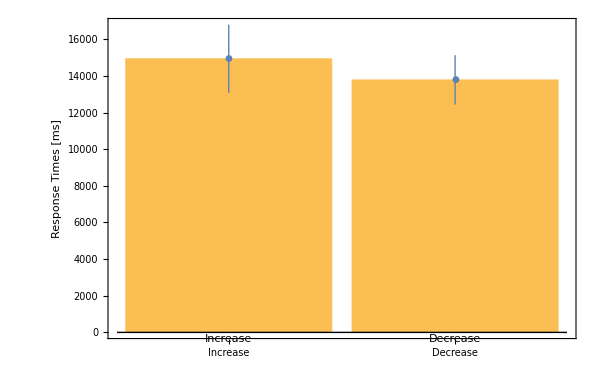

```mathematica
Show[BarChart[#[[;;,1,2]],ChartLabels->{"Increase","Decrease"},Frame-> {False,True,False,False}
 ,Axes->{True,False},BaseStyle->Directive[FontSize->18],FrameLabel->{None,"Response Times [ms]"},FrameStyle->20,ImageSize->600],ErrorListPlot[#,Frame-> {True,True,False,False},FrameLabel->{"QuestionType [angle/vertex]","Percent answers correct"},PlotStyle->Thick,PlotMarkers->Automatic]]&@SortBy[Join[{{#[[1,1]],N@Mean[#[[;;,2]]]},N@ErrorBar[StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]])]}&/@(GatherBy[Join@@Map[{If[#[[4]]=="increase",1,2],N@ToExpression@#[[7]]}&,DataCleanAllGradedNonExperts,{2}],First])],First]
```

```mathematica
MannWhitneyTest@(GatherBy[Join@@Map[{If[#[[4]]=="increase",1,2],N@ToExpression@#[[7]]}&,DataCleanAllGradedNonExperts,{2}],First])[[;;,;;,2]]
```

0.176667

#### Every Question Type Alone

```mathematica
rules={{"angle","increase","distance"}-> 1,{"angle","decrease","distance"}-> 2,{"angle","increase","angle"}-> 3,{"angle","decrease","angle"}->4,{"vertex","increase","distance"}->5,{"vertex","decrease","distance"}-> 6,{"vertex","increase","angle"}-> 7,{"vertex","decrease","angle"}-> 8};
```

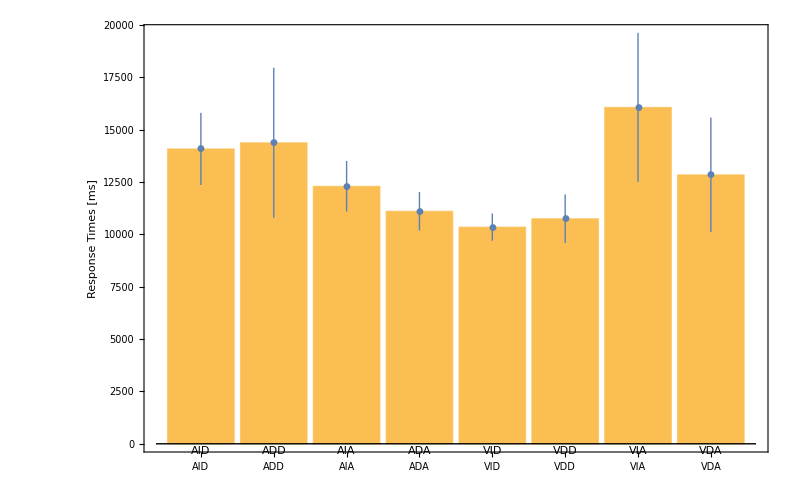

```mathematica
Show[BarChart[#[[;;,1,2]],Frame-> {False,True,False,False}
 ,Axes->{True,False},BaseStyle->Directive[FontSize->20],FrameLabel->{None,"Response Times [ms]"},FrameStyle->20,ChartLabels->{"AID","ADD","AIA","ADA","VID","VDD","VIA","VDA"},ImageSize->800],ErrorListPlot[#,Frame-> {True,True,False,False},PlotStyle->Thick,PlotMarkers->Automatic]]&@SortBy[Join[{{#[[1,1]],N@Mean[#[[;;,2]]]},N@ErrorBar[StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]]) ]}&/@(GatherBy[Join@@Map[{#[[{3,4,5}]],N@ToExpression@#[[7]]}&,DataCleanAllGradedNonExperts,{2}]/.rules,First])],First]
```

```mathematica
MannWhitneyTest@(SortBy[(GatherBy[Join@@Map[{#[[{3,4,5}]],N@ToExpression@#[[7]]}&,DataCleanAllGradedExperts,{2}]/.rules,First]),First][[{7,8},;;,2]])
```

0.334606

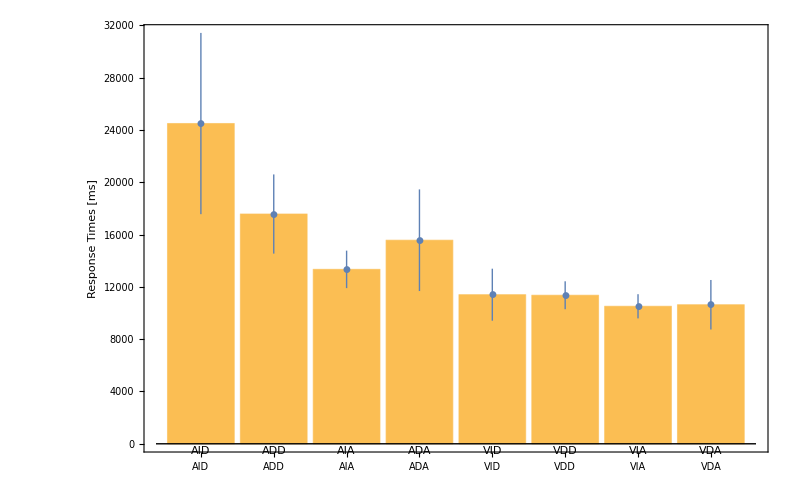

```mathematica
Show[BarChart[#[[;;,1,2]],Frame-> {False,True,False,False}
 ,Axes->{True,False},BaseStyle->Directive[FontSize->20],FrameLabel->{None,"Response Times [ms]"},FrameStyle->20,ChartLabels->{"AID","ADD","AIA","ADA","VID","VDD","VIA","VDA"},ImageSize->800],ErrorListPlot[#,Frame-> {True,True,False,False},PlotStyle->Thick,PlotMarkers->Automatic]]&@SortBy[Join[{{#[[1,1]],N@Mean[#[[;;,2]]]},N@ErrorBar[StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]]) ]}&/@(GatherBy[Join@@Map[{#[[{3,4,5}]],N@ToExpression@#[[7]]}&,DataCleanAllGradedExperts,{2}]/.rules,First])],First]
```

```mathematica
MannWhitneyTest@(SortBy[(GatherBy[Join@@Map[{#[[{3,4,5}]],N@ToExpression@#[[7]]}&,DataCleanAllGradedExperts,{2}]/.rules,First]),First][[{1,2},;;,2]])
```

0.77374

## Response times for first X questions

### Response times vs. Base length (perhaps a slight dependence on base length)

```mathematica
(*1=angle; 2=base factor; 3=Qtype; 4=Manipulation; 5=What's manipulated; 6=correct answer; 7=timing; 8=user answer; 9=correct/not*)
```

```mathematica
ErrorListPlot[#,Joined->True,PlotRange->{{0,1.1},{0,20 10^3}},Frame-> {True,True,False,False},FrameStyle-> 18,ImageSize-> 500,FrameLabel->{"Base Length","Response Times [msec]"},PlotStyle->Thick,PlotMarkers->Automatic]&@({{ToExpression@#[[1,1]],N@Mean[#[[;;,2]]]},ErrorBar[N@MedianDeviation[#[[;;,2]]]]}&/@
GatherBy[Join@@Map[{N@#[[2]],N@ToExpression@#[[7]]}&,DataCleanAllGradedNonExperts,{2}],First])
```

-Graphics-

### Response Times vs. Angle Size (mean - slight angle size dependence, median - no dependence on angle size)

```mathematica
ErrorListPlot[#,Joined->True,PlotRange->{{0,90},{0,20 10^3}},Frame-> {True,True,False,False},FrameStyle-> 18,ImageSize-> 500,FrameLabel->{"Base Length","Response Times [msec]"},PlotStyle->Thick,PlotMarkers->Automatic]&@({{ToExpression@#[[1,1]],N@Mean[#[[;;,2]]]},ErrorBar[N@(StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]]))]}&/@
SortBy[GatherBy[Join@@Map[{N@#[[1]],N@ToExpression@#[[7]]}&,DataCleanAllGradedNonExperts,{2}],First],First])
```

-Graphics-

```mathematica
MannWhitneyTest[SortBy[GatherBy[Join@@Map[{N@#[[1]],N@ToExpression@#[[7]]}&,DataCleanAllGradedNonExperts,{2}],First],First][[{1,3},;;,2]]]
```

0.284882

### Response Time vs. Side length

```mathematica
(*1=angle; 2=base factor; 3=Qtype; 4=Manipulation; 5=What's manipulated; 6=correct answer; 7=timing; 8=user answer; 9=correct/not*)
```

```mathematica
ErrorListPlot[#,(*Joined->True,*)PlotRange->{{0,2.2},{0,20 10^3}},Frame-> {True,True,False,False},FrameStyle-> 20,ImageSize-> 600,FrameLabel->{"Side Length","Response Times [msec]"},PlotStyle->Thick,PlotMarkers->Automatic]&@({{#[[1,1]],Median[#[[;;,2]]]},ErrorBar[N@MedianDeviation[#[[;;,2]]]]}&/@GatherBy[Join@@Map[{N@((ToExpression@#[[2]])/Cos[ToExpression@#[[1]] Degree]),N@ToExpression@#[[7]]}&,DataCleanAllGradedNonExperts,{2}],First])
```

-Graphics-

### Response Time vs. Question type

```mathematica
(*1=angle; 2=base factor; 3=Qtype; 4=Manipulation; 5=What's manipulated; 6=correct answer; 7=timing; 8=user answer; 9=correct/not*)
```

#### What’s being asked about

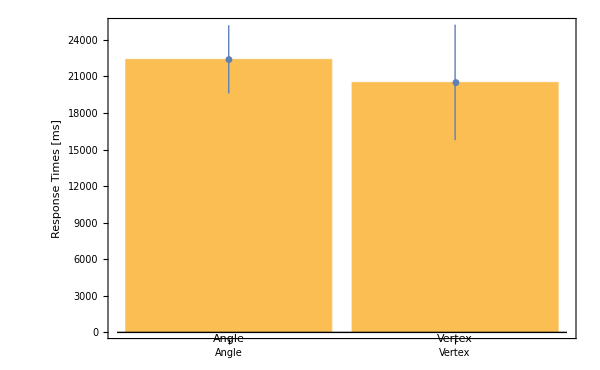

```mathematica
Show[BarChart[#[[;;,1,2]],ChartLabels->{"Angle","Vertex"},Frame-> {False,True,False,False}
 ,Axes->{True,False},BaseStyle->Directive[FontSize->16],FrameLabel->{None,"Response Times [ms]"},FrameStyle->18,ImageSize->600],ErrorListPlot[#,Frame-> {True,True,False,False},FrameLabel->{"QuestionType [angle/vertex]","Percent answers correct"},PlotStyle->Thick,PlotMarkers->Automatic]]&@SortBy[Join[{{#[[1,1]],N@Mean[#[[;;,2]]]},N@ErrorBar[StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]])]}&/@(GatherBy[Join@@Map[{If[#[[3]]=="angle",1,2],N@ToExpression@#[[7]]}&,DataCleanFirstQGradedNonExperts,{2}],First])],First]
```

```mathematica
MannWhitneyTest@(GatherBy[Join@@Map[{If[#[[3]]=="angle",1,2],N@ToExpression@#[[7]]}&,DataCleanFirstQGradedNonExperts,{2}],First])[[;;,;;,2]]
```

0.0372701

#### What’s being manipulated

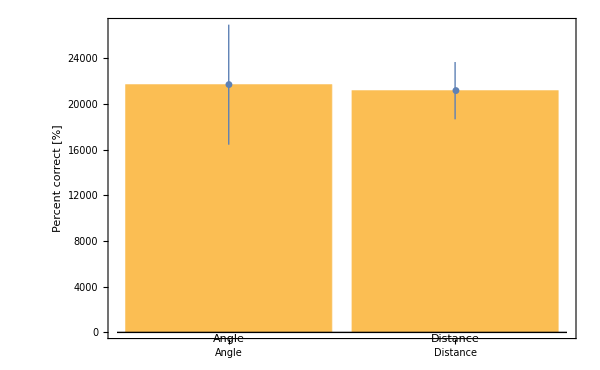

```mathematica
Show[BarChart[#[[;;,1,2]],ChartLabels->{"Angle","Distance"},Frame-> {False,True,False,False}
 ,Axes->{True,False},BaseStyle->Directive[FontSize->18],FrameLabel->{None,"Percent correct [%]"},FrameStyle->20,ImageSize->600],ErrorListPlot[#,Frame-> {True,True,False,False},FrameLabel->{"QuestionType [angle/vertex]","Percent answers correct"},PlotStyle->Thick,PlotMarkers->Automatic]]&@SortBy[Join[{{#[[1,1]],N@Mean[#[[;;,2]]]},N@ErrorBar[StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]])]}&/@(GatherBy[Join@@Map[{If[#[[5]]=="angle",1,2],N@ToExpression@#[[7]]}&,DataCleanFirstQGradedNonExperts,{2}],First])],First]
```

```mathematica
MannWhitneyTest@(GatherBy[Join@@Map[{If[#[[5]]=="angle",1,2],N@ToExpression@#[[7]]}&,DataCleanFirstQGradedNonExperts,{2}],First])[[;;,;;,2]]
```

0.374019

#### What’s the manipulation - Increase/Decrease (there is a trend)

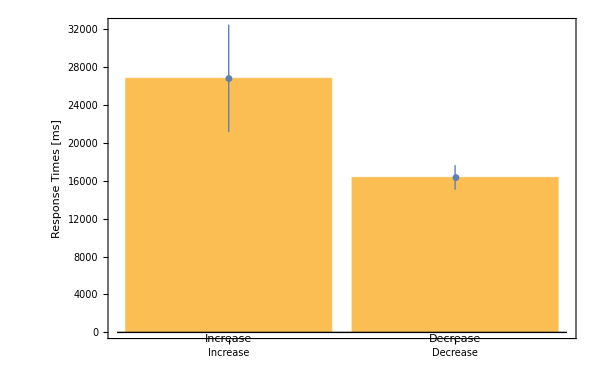

```mathematica
Show[BarChart[#[[;;,1,2]],ChartLabels->{"Increase","Decrease"},Frame-> {False,True,False,False}
 ,Axes->{True,False},BaseStyle->Directive[FontSize->18],FrameLabel->{None,"Response Times [ms]"},FrameStyle->20,ImageSize->600],ErrorListPlot[#,Frame-> {True,True,False,False},FrameLabel->{"QuestionType [angle/vertex]","Percent answers correct"},PlotStyle->Thick,PlotMarkers->Automatic]]&@SortBy[Join[{{#[[1,1]],N@Mean[#[[;;,2]]]},N@ErrorBar[StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]])]}&/@(GatherBy[Join@@Map[{If[#[[4]]=="increase",1,2],N@ToExpression@#[[7]]}&,DataCleanFirstQGradedNonExperts,{2}],First])],First]
```

```mathematica
MannWhitneyTest@(GatherBy[Join@@Map[{If[#[[4]]=="increase",1,2],N@ToExpression@#[[7]]}&,DataCleanFirstQGradedNonExperts,{2}],First])[[;;,;;,2]]
```

0.226862

#### Every Question Type Alone

```mathematica
rules={{"angle","increase","distance"}-> 1,{"angle","decrease","distance"}-> 2,{"angle","increase","angle"}-> 3,{"angle","decrease","angle"}->4,{"vertex","increase","distance"}->5,{"vertex","decrease","distance"}-> 6,{"vertex","increase","angle"}-> 7,{"vertex","decrease","angle"}-> 8};
```

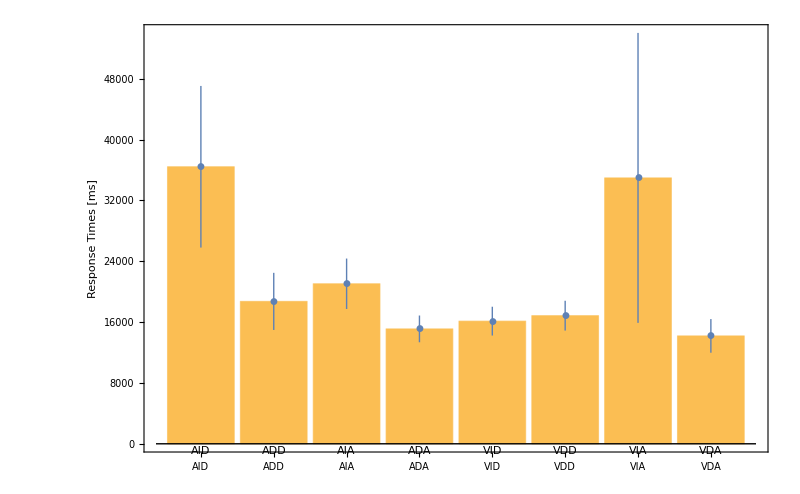

```mathematica
Show[BarChart[#[[;;,1,2]],Frame-> {False,True,False,False}
 ,Axes->{True,False},BaseStyle->Directive[FontSize->20],FrameLabel->{None,"Response Times [ms]"},FrameStyle->20,ChartLabels->{"AID","ADD","AIA","ADA","VID","VDD","VIA","VDA"},ImageSize->800],ErrorListPlot[#,Frame-> {True,True,False,False},PlotStyle->Thick,PlotMarkers->Automatic]]&@SortBy[Join[{{#[[1,1]],N@Mean[#[[;;,2]]]},N@ErrorBar[StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]]) ]}&/@(GatherBy[Join@@Map[{#[[{3,4,5}]],N@ToExpression@#[[7]]}&,DataCleanFirstQGradedNonExperts,{2}]/.rules,First])],First]
```

```mathematica
MannWhitneyTest@(SortBy[(GatherBy[Join@@Map[{#[[{3,4,5}]],N@ToExpression@#[[7]]}&,DataCleanAllGradedExperts,{2}]/.rules,First]),First][[{7,8},;;,2]])
```

0.334606

```mathematica
Show[BarChart[#[[;;,1,2]],Frame-> {False,True,False,False}
 ,Axes->{True,False},BaseStyle->Directive[FontSize->20],FrameLabel->{None,"Response Times [ms]"},FrameStyle->20,ChartLabels->{"AID","ADD","AIA","ADA","VID","VDD","VIA","VDA"},ImageSize->800],ErrorListPlot[#,Frame-> {True,True,False,False},PlotStyle->Thick,PlotMarkers->Automatic]]&@SortBy[Join[{{#[[1,1]],N@Mean[#[[;;,2]]]},N@ErrorBar[StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]]) ]}&/@(GatherBy[Join@@Map[{#[[{3,4,5}]],N@ToExpression@#[[7]]}&,DataCleanAllGradedExperts,{2}]/.rules,First])],First]
```

-Graphics-

```mathematica
MannWhitneyTest@(SortBy[(GatherBy[Join@@Map[{#[[{3,4,5}]],N@ToExpression@#[[7]]}&,DataCleanAllGradedExperts,{2}]/.rules,First]),First][[{1,2},;;,2]])
```

0.77374

## Analysis per Question Type

```mathematica
(*1=angle; 2=base factor; 3=timing; 4=user answer; 5=correct/not*)
```

```mathematica
DataPerQTypeAllNonExperts=(Sort@GatherBy[Join@@Map[{#[[3;;5]]/.rules,#[[{1,2,7,8,9}]]}&,DataCleanAllGradedNonExperts,{2}],First])[[;;,;;,2]];
DataPerQTypeAllExperts=(Sort@GatherBy[Join@@Map[{#[[3;;5]]/.rules,#[[{1,2,7,8,9}]]}&,DataCleanAllGradedExperts,{2}],First])[[;;,;;,2]];
QuestionType={"AID","ADD","AIA","ADA","VID","VDD","VIA","VDA"};
```

### Percent correct vs. Base length

```mathematica
(*1=angle; 2=base factor; 3=timing; 4=user answer; 5=correct/not*)
```

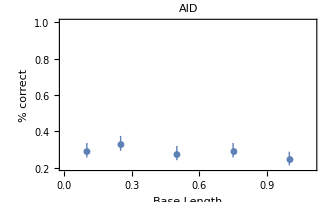
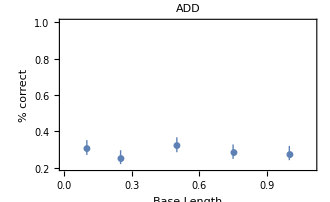
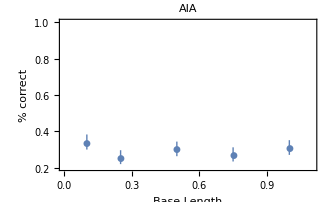
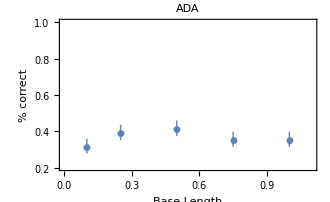
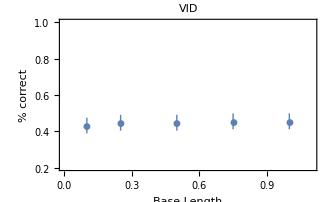
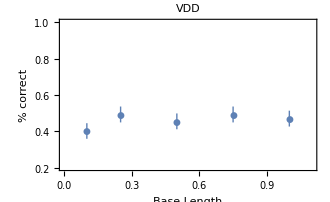
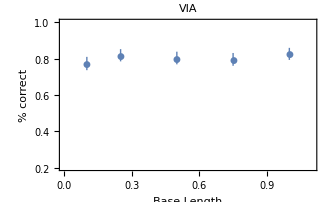
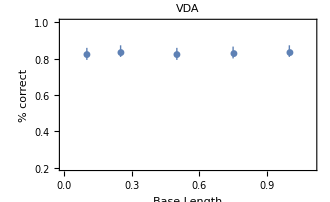

```mathematica
MapIndexed[ErrorListPlot[#1,PlotRange->{{0,1.1},{0.2,1}},PlotLabel->QuestionType[[#2[[1]]]], Frame-> {True,True,False,False},FrameLabel->{"Base Length","% correct"},PlotStyle->Thick,PlotMarkers->Automatic,FrameStyle->16,ImageSize->330]&,(SortBy[#,First]&/@Map[{{ToExpression@#[[1,1]],N@Mean[#[[;;,2]]]},ErrorBar[N@(StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]]))]}&,(GatherBy[#,First]&/@Map[{N@#[[2]],N@#[[-1]]}&,DataPerQTypeAllNonExperts,{2}]),{2}]),{1}]
```

```mathematica
Manipulate[ErrorListPlot[Evaluate@#,PlotRange->{{0,1.1},{PerLow,PerHigh}},PlotLabel->QuestionType[[{i,j}]], Frame-> {True,True,False,False},FrameLabel->{"Base Length","% correct"},PlotStyle->Thick,PlotMarkers->Automatic,FrameStyle->16,ImageSize->600]&@(SortBy[#,First]&/@Map[{{ToExpression@#[[1,1]],N@Mean[#[[;;,2]]]},ErrorBar[N@(StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]]))]}&,(GatherBy[#,First]&/@Map[{N@#[[2]],N@#[[-1]]}&,DataPerQTypeAll,{2}]),{2}])[[{i,j}]],{{i,1},1,8,1},{{j,2},1,8,1},{{PerLow,0.3},0.2,1},{{PerHigh,0.8},0.4,1}]
```

Part::partd: Part specification DataPerQTypeAll⟦{1,2}⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ListPlot::lpn: DataPerQTypeAll⟦{1,2}⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

### Percent correct vs. Angle Size (decreasing on AID, ADD, AIA?,VDD // Increasing - VID, VIA))- Angles matter (not Euclidian!)

```mathematica
(*1=angle; 2=base factor; 3=timing; 4=user answer; 5=correct/not*)
```

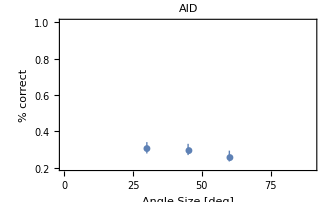
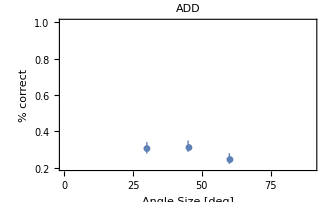
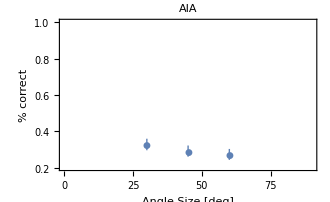
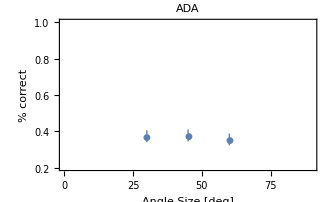
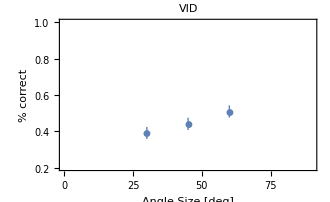
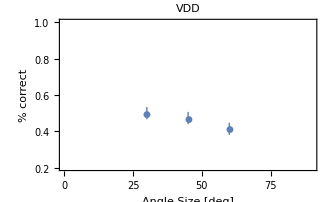
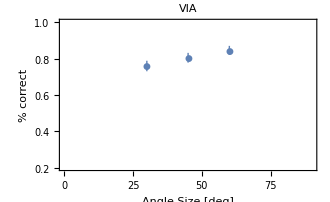
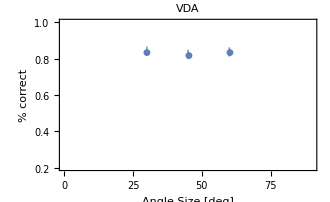

```mathematica
MapIndexed[ErrorListPlot[#1,PlotRange->{{0,90},{0.2,1}},PlotLabel->QuestionType[[#2[[1]]]], Frame-> {True,True,False,False},FrameLabel->{"Angle Size [deg]","% correct"},PlotStyle->Thick,PlotMarkers->Automatic,FrameStyle->16,ImageSize->330]&,(SortBy[#,First]&/@Map[{{ToExpression@#[[1,1]],N@Mean[#[[;;,2]]]},ErrorBar[N@(StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]]))]}&,(GatherBy[#,First]&/@Map[{N@#[[1]],N@#[[-1]]}&,DataPerQTypeAllNonExperts,{2}]),{2}]),{1}]
```

```mathematica
Manipulate[ErrorListPlot[Evaluate@#,PlotRange->{{0,90},{PerLow,PerHigh}},PlotLabel->QuestionType[[{i,j}]], Frame-> {True,True,False,False},FrameLabel->{"Angle Size [deg]","% correct"},PlotStyle->Thick,PlotMarkers->Automatic,FrameStyle->16,ImageSize->600]&@(SortBy[#,First]&/@Map[{{ToExpression@#[[1,1]],N@Mean[#[[;;,2]]]},ErrorBar[N@(StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]]))]}&,(GatherBy[#,First]&/@Map[{N@#[[1]],N@#[[-1]]}&,DataPerQTypeAllNonExperts,{2}]),{2}])[[{i,j}]],{{i,1},1,8,1},{{j,2},1,8,1},{{PerLow,0.2},0.2,1},{{PerHigh,0.8},0.4,1}]
```

Part::partd: Part specification DataPerQTypeAllNonExperts⟦{1,2}⟧ is longer than depth of object.

ListPlot::lpn: DataPerQTypeAllNonExperts⟦{1,2}⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

### Response times vs. Base length

```mathematica
(*1=angle; 2=base factor; 3=timing; 4=user answer; 5=correct/not*)
```

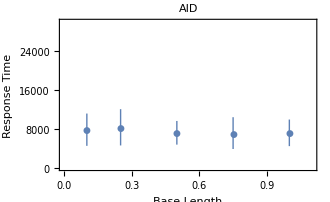
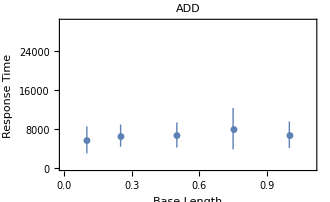
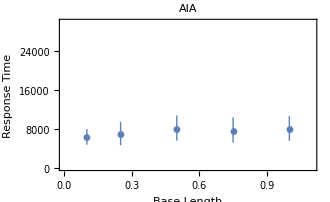
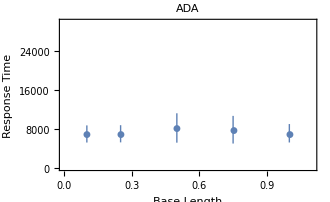
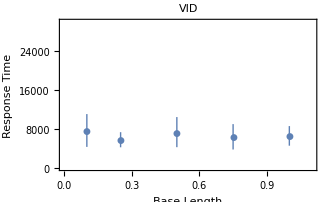
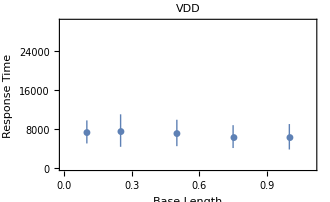
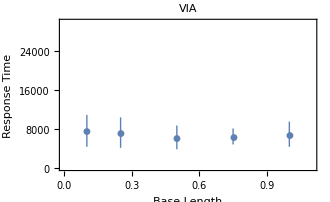
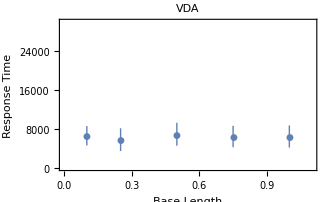

```mathematica
MapIndexed[ErrorListPlot[#1,PlotRange->{{0,1.1},{0,30 10^3}},PlotLabel->QuestionType[[#2[[1]]]], Frame-> {True,True,False,False},FrameLabel->{"Base Length","Response Time"},PlotStyle->Thick,PlotMarkers->Automatic,FrameStyle->16,ImageSize->330]&,(SortBy[#,First]&/@Map[{{ToExpression@#[[1,1]],N@Median[#[[;;,2]]]},ErrorBar[N@MedianDeviation[#[[;;,2]]]]}&,(GatherBy[#,First]&/@Map[{N@#[[2]],N@ToExpression@#[[3]]}&,DataPerQTypeAllExperts,{2}]),{2}]),{1}]
```

```mathematica
Manipulate[ErrorListPlot[#,PlotRange->{{0,1.1},{PerLow 10^3,PerHigh 10^3}},PlotLabel->QuestionType[[{i,j}]], Frame-> {True,True,False,False},FrameLabel->{"Base Length","Response Times [ms]"},PlotStyle->Thick,PlotMarkers->Automatic,FrameStyle->16,ImageSize->600]&@(SortBy[#,First]&/@Map[{{ToExpression@#[[1,1]],N@f[#[[;;,2]]]},ErrorBar[N@MedianDeviation@#[[;;,2]]]}&,(GatherBy[#,First]&/@Map[{N@#[[2]],N@ToExpression@#[[3]]}&,DataPerQTypeAllExperts,{2}]),{2}])[[{i,j}]],{{i,1},1,8,1},{{j,2},1,8,1},{{PerLow,2},1,6},{{PerHigh,15},8,40},{f,{Median,Mean}}]
```

### Response times vs. Angle Size

```mathematica
(*1=angle; 2=base factor; 3=timing; 4=user answer; 5=correct/not*)
```

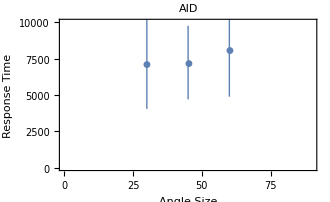
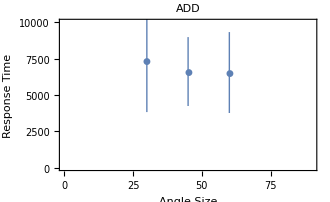
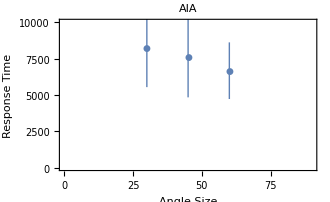
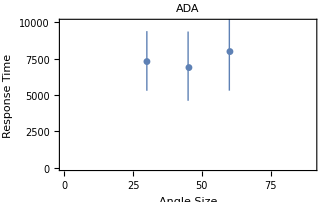
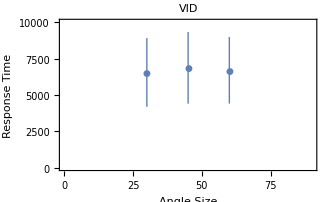
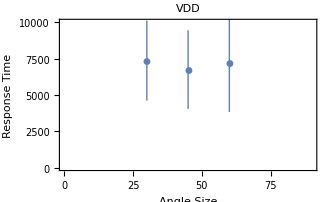
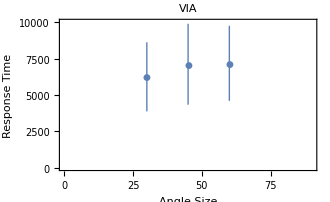
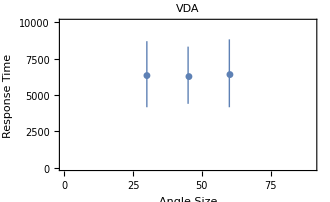

```mathematica
MapIndexed[ErrorListPlot[#1,PlotRange->{{0,90},{0,10 10^3}},PlotLabel->QuestionType[[#2[[1]]]], Frame-> {True,True,False,False},FrameLabel->{"Angle Size","Response Time"},PlotStyle->Thick,PlotMarkers->Automatic,FrameStyle->16,ImageSize->330]&,(SortBy[#,First]&/@Map[{{ToExpression@#[[1,1]],N@Median[#[[;;,2]]]},ErrorBar[N@MedianDeviation[#[[;;,2]]]]}&,(GatherBy[#,First]&/@Map[{N@#[[1]],N@ToExpression@#[[3]]}&,DataPerQTypeAllExperts,{2}]),{2}]),{1}]
```

```mathematica
Manipulate[ErrorListPlot[#,PlotRange->{{0,90},{PerLow 10^3,PerHigh 10^3}},PlotLabel->QuestionType[[{i,j}]], Frame-> {True,True,False,False},FrameLabel->{"Angle Size","Response Times [ms]"},PlotStyle->Thick,PlotMarkers->Automatic,FrameStyle->16,ImageSize->600]&@(SortBy[#,First]&/@Map[{{ToExpression@#[[1,1]],N@f[#[[;;,2]]]},ErrorBar[N@MedianDeviation@#[[;;,2]]]}&,(GatherBy[#,First]&/@Map[{N@#[[1]],N@ToExpression@#[[3]]}&,DataPerQTypeAllExperts,{2}]),{2}])[[{i,j}]],{{i,1},1,8,1},{{j,2},1,8,1},{{PerLow,2},1,6},{{PerHigh,10},8,40},{f,{Median,Mean}}]
```